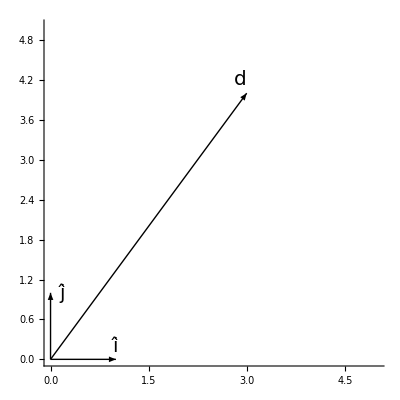

```mathematica
Graphics[{Arrow[{{0,0},#}]& /@{{3,4},{1,0},{0,1}},Text[Style[OverHat["i"], FontFamily->"Times New Roman",FontSize->20],{1,0.2}],Text[Style[OverHat["j"], FontFamily->"Times New Roman",FontSize->20],{0.2,1}],
Text[Style["d", FontFamily->"Times New Roman",FontSize->20],{2.9,4.2}]},Axes->True,PlotRange->{{0,5},{0,5}}]
```

```mathematica
PiX[x_]:=Module[{k=x,q=0,l=1},
While[l≤k,q++;l=NextPrime[l]];Return[q];
]
```

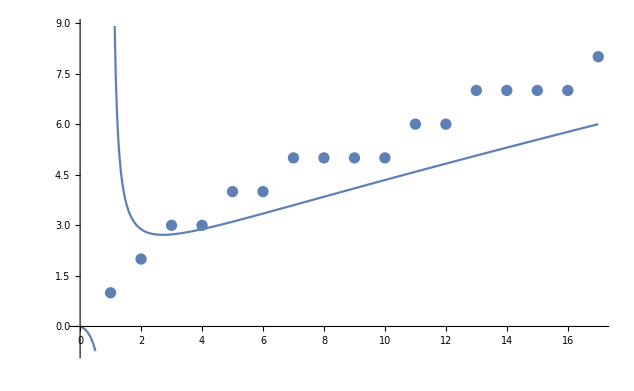

```mathematica
Show[Plot[x/Log[x],{x,0,17}],
ListPlot[Table[PiX@i,{i,17}]]]
```